```mathematica
ASSETSDIR = 
       "C:\\Users\\Bruno\\PycharmProjects\\mhack\\buffer\\"; 
FILENAME = "input.json"; 
jsonimport[] := Association[Import[StringJoin[ASSETSDIR, FILENAME]]]
```

```mathematica
IN=jsonimport[];
```

```mathematica
(***************************************************************)
```

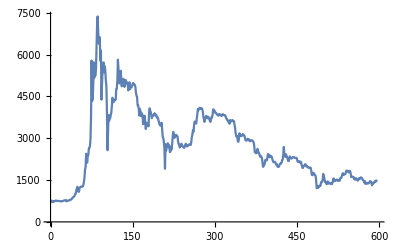

```mathematica
OutputGraphics = ListLinePlot[IN["bitcoinPrice"], PlotTheme -> "Simple"]
```

```mathematica
(**************************************************************)
```

```mathematica
Export[ASSETSDIR<>IN["META_OUTPUT_FILENAME"],OutputGraphics];
```